# Parrondo’s paradox and agriculture

## Impact of pathogen

```mathematica
sqmax=10;
a=1;b=1;
θ=3;
g=1;
pathogenmax=10;
pcovermax=0.4;
p1=0;
p2=0.8;
```

## Analytics

```mathematica
PTpdf[i_,γ_,PTmax_]:=((1-γ)/γ)^i/(∑_(j=0)^PTmax ((1-γ)/γ)^j);
Sqpdf[i_,γ_,k_]:=(γ/(1-γ))^i/(∑_(j=0)^k (γ/(1-γ))^j);
p2eff[γ_,p2max_,α_,PTmax_]:=p2max(1-α∑_(i=0)^PTmax i PTpdf[i,γ,PTmax]/PTmax);
p1eff[γ_,p1max_,α_,PTmax_]:=p1max(1-α∑_(i=0)^PTmax i PTpdf[i,γ,PTmax]/PTmax);
peff[γ_,pmax_,α_,PTmax_]:=pmax(1-α∑_(i=0)^PTmax i PTpdf[i,γ,PTmax]/PTmax);
```

```mathematica
q1eff[γ_,pmax_,p1max_,p2max_,α_,PTmax_]:=γ peff[γ,pmax,α,PTmax]+(1-γ) p1eff[γ,p1max,α,PTmax];
q2eff[γ_,pmax_,p1max_,p2max_,α_,PTmax_]:=γ peff[γ,pmax,α,PTmax]+(1-γ) p2eff[γ,p2max,α,PTmax];
```

```mathematica
Pwineff[γ_,pmax_,p1max_,p2max_,α_,PTmax_,θ_,k_]:= q1eff[γ,pmax,p1max,p2max,α,PTmax]∑_(i=0)^θ Sqpdf[i,γ,k]+ q2eff[γ,pmax,p1max,p2max,α,PTmax]∑_(i=θ+1)^k Sqpdf[i,γ,k];
```

```mathematica
γ=.;α=.;
analyticspl=Plot[Evaluate[Table[Callout[Pwineff[γ,pcovermax,p1,p2,α,pathogenmax,θ,sqmax],"α = "<>ToString[α],Above],{α,{0,0.5,1}}]],{γ,0,1},GridLines->{{0.5}, {0.5}},PlotRange->{{0,1},{0,0.6}},
PlotStyle->{Directive[Darker[Blue],Opacity[0.25]],Directive[Darker[Blue],Opacity[0.5]],Directive[Darker[Blue]]}];
```

-Graphics-

```mathematica
Show[analyticspl,GridLinesStyle->Directive[Black, Dashed,Thickness[0.005]],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Frequency of cover crops (γ)",14,Black],Style["Probability of making a profit",14,Black]},PlotRange->{{0,1},{-0.05,0.6}}]
```

-Graphics-

```mathematica
Table[Callout[{γ/.FindMaximum[Pwineff[γ,pcovermax,p1,p2,α,pathogenmax,θ,sqmax],{γ,0.0001,0.999}]⟦2⟧,FindMaximum[Pwineff[γ,pcovermax,p1,p2,α,pathogenmax,θ,sqmax],{γ,0.0001,0.999}]⟦1⟧},"α = "<>ToString[α]],{α,{0.0001,0.2,0.4,0.6,0.8,0.999}}]
```

{Callout[{0.602635,0.54482},α = 0.0001],Callout[{0.62248,0.526844},α = 0.2],Callout[{0.641794,0.51207},α = 0.4],Callout[{0.660187,0.499788},α = 0.6],Callout[{0.677544,0.489429},α = 0.8],Callout[{0.693776,0.480609},α = 0.999]}

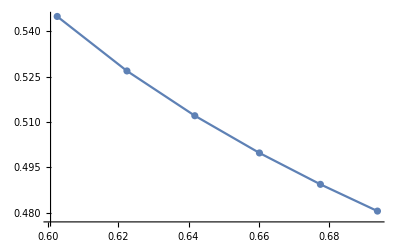

```mathematica
ListPlot[Table[{γ/.FindMaximum[Pwineff[γ,pcovermax,p1,p2,α,pathogenmax,θ,sqmax],{γ,0.0001,0.999}]⟦2⟧,FindMaximum[Pwineff[γ,pcovermax,p1,p2,α,pathogenmax,θ,sqmax],{γ,0.0001,0.999}]⟦1⟧},{α,{0.0001,0.2,0.4,0.6,0.8,0.999}}],Joined->True,Mesh->All]
```

```mathematica
ListPlot[Table[Callout[{γ/.FindMaximum[Pwineff[γ,pcovermax,p1,p2,α,pathogenmax,θ,sqmax],{γ,0.0001,0.999}]⟦2⟧,FindMaximum[Pwineff[γ,pcovermax,p1,p2,α,pathogenmax,θ,sqmax],{γ,0.0001,0.999}]⟦1⟧},"α = "<>ToString[α]],{α,{0.0001,0.2,0.4,0.6,0.8,0.999}}],Joined->True,PlotRange->{{0.45,0.75},{0.45,0.75}},Mesh->All,GridLines->{{-1,0,0.5,1}, {-1,0,0.5,1}},GridLinesStyle->Directive[Black, Dashed,Thickness[0.005]],AspectRatio->1,Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],FrameLabel->{Style["Optimum cover crop fraction (γ_max)",Black,16],Style["Maximum probability of winning (P_win)",Black,16]}]
```

-Graphics-

## Different versions of including pathogen dynamics

#### A simple single run to show the effect of pathogens on the yield

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
dynamicalphas={};
For[α=0,α≤1,α=α+0.5,
sequence=RandomChoice[{1-0.6,0.6}->{"cash","cover"},1000];
pathogeninit=2;
winninginit=0;
sqinit=0;
Clear[dynamics];
dynamics={{pathogeninit,sqinit,winninginit}};
For[i=1,i≤Length[sequence],i++,
croptype=sequence⟦i⟧;

pathogen=pathogeninit+(Switch[croptype,"cover",If[pathogeninit≤0,0,-g] ,"cash", If[pathogeninit≥pathogenmax,0,g]]);

sq=sqinit+Switch[croptype,"cover",If[sqinit≥sqmax,0,a],
"cash",
If[sqinit≤0,0,-b]
];


winning=winninginit+If[RandomReal[]<Switch[croptype,"cover",pcovermax (1-α pathogeninit/pathogenmax),
"cash",
If[sqinit<θ,p1 (1- α pathogeninit/pathogenmax),
p2 (1-α pathogeninit/pathogenmax)]
],+1,-1];

pathogeninit=pathogen;
sqinit=sq;
winninginit=winning;

AppendTo[dynamics,{pathogeninit,sqinit,winninginit}];
];
AppendTo[dynamicalphas,dynamics]
]
```

```mathematica
dynamicalphas⟦1⟧
```

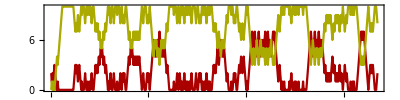
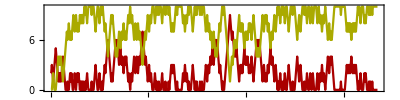
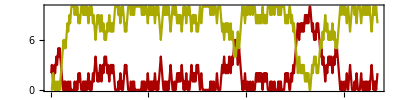

```mathematica
{ListPlot[Transpose[dynamicalphas⟦1⟧]⟦1;;2⟧,Joined->True,PlotStyle->{Darker[Red],Darker[Yellow]},Frame->True,FrameStyle->Directive[Thickness[0.003],Black],AspectRatio->0.25],
ListPlot[Transpose[dynamicalphas⟦2⟧]⟦1;;2⟧,Joined->True,PlotStyle->{Darker[Red],Darker[Yellow]},Frame->True,FrameStyle->Directive[Thickness[0.003],Black],AspectRatio->0.25],
ListPlot[Transpose[dynamicalphas⟦3⟧]⟦1;;2⟧,Joined->True,PlotStyle->{Darker[Red],Darker[Yellow]},Frame->True,FrameStyle->Directive[Thickness[0.003],Black],AspectRatio->0.25]}
```

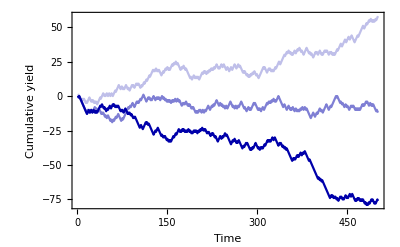

```mathematica
Show[{ListPlot[Transpose[dynamicalphas⟦1⟧]⟦3⟧,Joined->True,PlotStyle->{Directive[Darker[Blue],Opacity[0.25]]},Frame->True,FrameStyle->Directive[Thickness[0.003],Black],FrameLabel->{Style["Time",14,Black],Style["Cumulative yield",14,Black]}],
ListPlot[Transpose[dynamicalphas⟦2⟧]⟦3⟧,Joined->True,PlotStyle->{Directive[Darker[Blue],Opacity[0.5]]},Frame->True,FrameStyle->Directive[Thickness[0.003],Black],FrameLabel->{Style["Time",14,Black],Style["Cumulative yield",14,Black]}],
ListPlot[Transpose[dynamicalphas⟦3⟧]⟦3⟧,Joined->True,PlotStyle->{Directive[Darker[Blue]]},Frame->True,FrameStyle->Directive[Thickness[0.003],Black],FrameLabel->{Style["Time",14,Black],Style["Cumulative yield",14,Black]}]},PlotRange->All
]
```

#### Ensemble

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
bestFitSlope[data_]:=Module[{lm,x},lm=LinearModelFit[data,{1,x},x];
First@Pick[lm["BestFitParameters"],lm["BasisFunctions"],x]
];
```

```mathematica
alldistributions={};
allslopes={};
alphalist=Table[i,{i,0,1,0.1}];
For[αcounter=1,αcounter<=Length[alphalist],αcounter=αcounter+1,
α=alphalist⟦αcounter⟧;
meanplots={};
slopes={};
For[γ=0.1,γ<=0.9,γ=γ+0.1,
ensemble={};
ensemblepathogen={};
ensemblesoilsq={};
For[j=1,j≤500,j++;
sequence=RandomChoice[{1-γ,γ}->{"cash","cover"},1000];
pathogeninit=0;
winninginit=0;
sqinit=0;
Clear[dynamics];
dynamics={{pathogeninit,sqinit,winninginit}};
For[i=1,i≤Length[sequence],i++,
croptype=sequence⟦i⟧;

pathogen=pathogeninit+(Switch[croptype,"cover",If[pathogeninit≤0,0,-g] ,"cash", If[pathogeninit≥pathogenmax,0,g]]);

sq=sqinit+Switch[croptype,"cover",If[sqinit≥sqmax,0,a],
"cash",
If[sqinit≤0,0,-b]
];


winning=winninginit+If[RandomReal[]<Switch[croptype,"cover",pcovermax (1-α pathogeninit/pathogenmax),
"cash",
If[sqinit<θ,p1 (1- α pathogeninit/pathogenmax),
p2 (1-α pathogeninit/pathogenmax)]
],+1,-1];

pathogeninit=pathogen;
sqinit=sq;
winninginit=winning;

AppendTo[dynamics,{pathogeninit,sqinit,winninginit}];
];
AppendTo[ensemble,dynamics⟦All,3⟧];
AppendTo[ensemblepathogen,dynamics⟦All,1⟧];
AppendTo[ensemblesoilsq,dynamics⟦All,2⟧];
];
average=Mean[ensemble];
averagepath=Mean[ensemblepathogen];
averagesq=Mean[ensemblesoilsq];
AppendTo[slopes,(bestFitSlope[average⟦-50;;⟧]+1)/2];
AppendTo[meanplots,ensemble⟦All,Length[sequence]+1⟧(*{,ListPlot[average,Joined->True],ListPlot[averagepath,Joined->True],ListPlot[averagesq,Joined->True],ListPlot[{averagepath,averagesq}/10,Joined->True]}*)];
];
AppendTo[alldistributions,meanplots];
AppendTo[allslopes,slopes];
]
```

```mathematica
gammas=Table[i,{i,0.1,0.9,0.1}];
alphas=Table[i,{i,0,1,0.1}];
```

```mathematica
Manipulate[ListPlot[allslopes⟦j⟧,Joined->True,DataRange->{0.1,0.9},GridLines->{{-1,0,0.5,1}, {-1,0,0.5,1}},PlotRange->{{0,1},{0,0.6}},Epilog->{Inset[gammas⟦Position[allslopes⟦j⟧,Max[allslopes⟦j⟧]]⟦1⟧⟧⟦1⟧,{0.8,0.1}],Inset[Max[allslopes⟦j⟧],{0.8,0.05}]}],{j,1,Length[allslopes],1}]
```

Part::partd: Part specification allslopes⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of Symbol[] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: allslopes⟦1⟧ is not a list of numbers or pairs of numbers.

```mathematica
Show[analyticspl,ListPlot[{allslopes⟦1⟧,allslopes⟦6⟧,allslopes⟦11⟧},Joined->False,DataRange->{0.1,0.9},GridLines->{{0.5}, {0.5}},PlotMarkers->"OpenMarkers",PlotStyle->{Directive[PointSize[Medium],Darker[Blue],Opacity[0.25]],Directive[PointSize[Medium],Darker[Blue],Opacity[0.5]],Directive[PointSize[Medium],Darker[Blue]]}],GridLinesStyle->Directive[Black, Dashed,Thickness[0.005]],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Frequency of cover crops (γ)",14,Black],Style["Probability of making a profit",14,Black]},PlotRange->{{0,1},{-0.05,0.6}}]
```

-Graphics-

```mathematica
ListPlot[Table[Callout[{gammas⟦Position[allslopes⟦j⟧,Max[allslopes⟦j⟧]]⟦1⟧⟧⟦1⟧,Max[allslopes⟦j⟧]},"α = "<>ToString[alphas⟦j⟧]],{j,1,Length[allslopes]}],Joined->True,PlotRange->{{0.45,0.75},{0.45,0.75}},Mesh->All,GridLines->{{-1,0,0.5,1}, {-1,0,0.5,1}},GridLinesStyle->Directive[Black, Dashed,Thickness[0.005]],AspectRatio->1,Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],FrameLabel->{Style["Optimum cover crop fraction (γ_max)",Black,16],Style["Maximum probability of winning (P_win)",Black,16]}]
```

-Graphics-

```mathematica
meanplots⟦1⟧
```

100

```mathematica
Manipulate[ListPlot[meanplots⟦j⟧,Joined->True,DataRange->{0.1,0.9},GridLines->{{-1,0,0.5,1}, {-1,0,0.5,1}},PlotRange->{{0,1},{0,0.6}},Epilog->{Inset[0.1+0.05Position[allslopes⟦j⟧,Max[allslopes⟦j⟧]]⟦1⟧,{0.8,0.1}],Inset[Max[allslopes⟦j⟧],{0.8,0.05}]}],{j,1,Length[allslopes],1}]
```

```mathematica
(bestFitSlope[average⟦-50;;⟧]+1)/2
```

0.535771

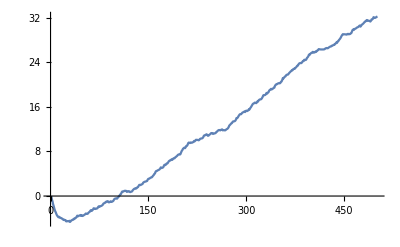

```mathematica
ListPlot[average,Joined->True]
```

```mathematica
alldistributions⟦1⟧
```

{{58,52,46,50,22,-4,60,60,54,52,46,22,68,10,40,82,10,16,58,24,28,44,46,-4,38,52,52,30,14,14,32,70,34,46,-20,44,-4,56,16,42,34,14,26,24,24,8,28,52,26,36,44,32,34,0,72,-24,24,62,70,6,36,20,12,26,34,4,4,26,18,46,22,-32,42,30,12,22,32,40,66,36,10,-8,68,54,24,16,26,22,54,-24,66,24,74,34,70,56,40,12,48,12}}

```mathematica
wins={};
If[#>0,AppendTo[wins,#]]&/@alldistributions⟦1,1⟧;
```

```mathematica
(wins//Length)/Length[alldistributions⟦1,1⟧]//N
```

0.91

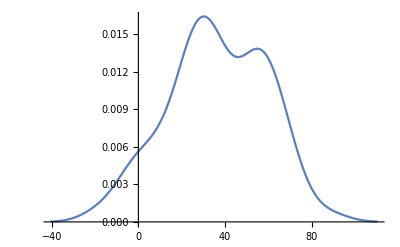

```mathematica
SmoothHistogram[alldistributions⟦1,7⟧]
```

```mathematica
alphas={0.1};
```

```mathematica
Manipulate[SmoothHistogram[Table[Callout[alldistributions⟦i⟧⟦j⟧,"α = "<>ToString[alphas⟦i⟧],Above],{i,1,3,1}],Frame->True,Filling->Axis,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Long term winnings",Black,18]},PlotLabel->Style["Long term winning distributions",Black,18],PlotRange->{{-500,200},Full},Epilog->Inset[Style["γ = "<>ToString[(j-1)/10//N],18,Black],{-400,0.018}]],{j,1,11,1}]
```

Part::partw: Part 2 of {{{-500,-500,-500,-500,-500,-500,-500,-500,-500,-500,«90»},{-464,-458,-472,-452,-458,-464,-468,-480,-468,-466,«90»},{-418,-418,-424,-384,-420,-434,-410,-412,-402,-426,«90»},«5»,{-26,-6,10,-10,-34,-46,-22,-12,-48,-16,«90»},{-50,-72,-76,-74,-58,-70,-120,-38,-54,-48,«90»},«1»}} does not exist.

Part::partw: Part 2 of {0.1} does not exist.

Part::partw: Part 3 of {{{-500,-500,-500,-500,-500,-500,-500,-500,-500,-500,«90»},{-464,-458,-472,-452,-458,-464,-468,-480,-468,-466,«90»},{-418,-418,-424,-384,-420,-434,-410,-412,-402,-426,«90»},«5»,{-26,-6,10,-10,-34,-46,-22,-12,-48,-16,«90»},{-50,-72,-76,-74,-58,-70,-120,-38,-54,-48,«90»},«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of {{{58,52,46,50,22,-4,60,60,54,52,«90»}}} does not exist.

Part::partw: Part 2 of {0.1} does not exist.

Part::partw: Part 3 of {{{58,52,46,50,22,-4,60,60,54,52,«90»}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of {0.1} does not exist.

Part::partw: Part 3 of {0.1} does not exist.

Part::partd: Part specification alldistributions⟦1⟧ is longer than depth of object.

Part::partd: Part specification alphas⟦1⟧ is longer than depth of object.

Part::partd: Part specification alldistributions⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification alphas⟦1⟧ is longer than depth of object.

Part::partd: Part specification alphas⟦2⟧ is longer than depth of object.

Part::partd: Part specification alphas⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification alphas⟦1⟧ is longer than depth of object.

Part::partd: Part specification alphas⟦2⟧ is longer than depth of object.

Part::partd: Part specification alphas⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification alphas⟦1⟧ is longer than depth of object.

Part::partd: Part specification alphas⟦2⟧ is longer than depth of object.

Part::partd: Part specification alphas⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Manipulate[SmoothHistogram[Table[Callout[alldistributions⟦j⟧⟦i⟧,"γ = "<>ToString[(i-1)/10//N],Above],{i,2,Length[alldistributions⟦j⟧],1}],Frame->True,Filling->Axis,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Long term winnings",Black,18]},PlotLabel->Style["Long term winning distributions",Black,18],PlotRange->{{-500,200},Full}],{j,1,3,1}]
```

Part::partd: Part specification alldistributions⟦1⟧ is longer than depth of object.

```mathematica
SmoothHistogram[Table[Callout[alldistributions⟦3⟧⟦i⟧,"γ = "<>ToString[(i-1)/10//N],Above],{i,2,Length[alldistributions⟦3⟧],1}],Frame->True,Filling->Axis,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Long term winnings",Black,18]},PlotLabel->Style["Long term winning distributions",Black,18],PlotRange->{{-500,200},Full},AspectRatio->0.5]
```

-Graphics-

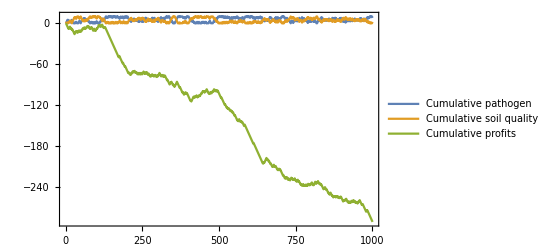

```mathematica
ListPlot[dynamics//Transpose,Joined->True,PlotLegends->{"Cumulative pathogen","Cumulative soil quality","Cumulative profits"},PlotRange->All,Frame->True]
```

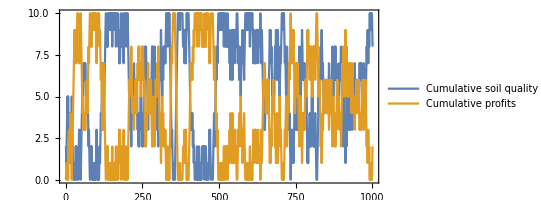

```mathematica
ListPlot[Transpose[dynamics⟦All,1;;2⟧],Joined->True,PlotLegends->{"Cumulative soil quality","Cumulative profits"},AspectRatio->1/2,Frame->True]
```

```mathematica
ensemble⟦1⟧
```

{1,105501}

```mathematica
ListPlot[ensemble,Joined->True,PlotRange->All,Frame->True]
```